```mathematica
Solve[(C-c)/t==q-(k *((C-c)/2)), C]
```

{{C→(2 c+c k t+2 q t)/(2+k t)}}

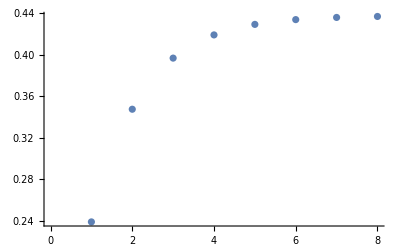

```mathematica
num=ListPlot[{0.23913826245327652,
0.34765071442625767,
0.3968898119775714,
0.4192327660218821,
0.4293712051942479,
0.433971668886198,
0.43605919595236003,
0.43700644160926727}]
```

```mathematica
c= (Co-q/k) Exp[-k t] +q/k
```

q/k+ⅇ^(-k t) (Co-q/k)

```mathematica
cval = c /. {q->(14716*.000022354),k-> .7515, Co->0}
```

0.43774-0.43774 ⅇ^(-0.7515 t)

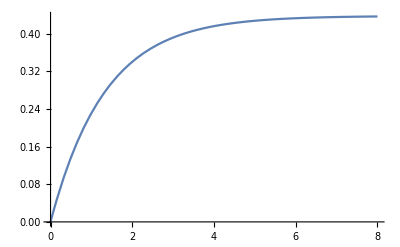

```mathematica
ana=Plot[cval,{t,0,8}]
```

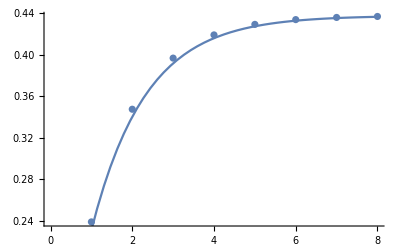

```mathematica
Show[{num,ana}]
```

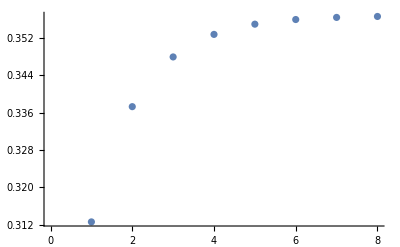

```mathematica
ListPlot[{0.31260610041849946,
0.337252432292013,
0.3478841173469304,
0.35270579922994,
0.3548936950152265,
0.3558864843752476,
0.3563369769337302,
0.3565413944602888}]
```

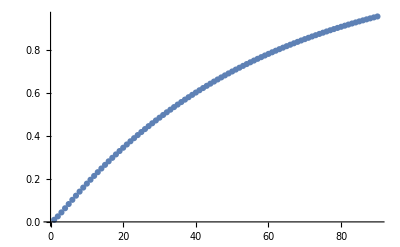

```mathematica
ListPlot[{0.009849885883875031,0.025746250538637765,0.04418473206163544,0.06357873082755837,0.08321179692103073,0.102762261859279,0.12208753443437963,0.14112622289342452,0.15985372250812363,0.1782620638211401,0.19635076950788571,0.2141227065392568,0.23158220501702287,0.2487342055275506,0.26558387318370336,0.2821364234166383,0.29839704383585625,0.31437085966556916,0.3300629189386934,0.3454781866406686,0.3606215428991805,0.3754977829948296,0.3901116181834029,0.40446767687200336,0.4185705059415831,0.4324245721219947,0.44603426337720353,0.45940389028168405,0.472537687379623,0.4854398145233634,0.4981143581896984,0.510565332773609,0.5227966818594815,0.5348122794700374,0.5466159312932966,0.5582113758879244,0.5696022858673305,0.5807922690628876,0.5917848696666334,0.6025835693538178,0.6131917883856511,0.6236128866925982,0.6338501649385664,0.6439068655663217,0.653786173824464,0.6634912187762878,0.6730250742908468,0.6823907600165381,0.6915912423375117,0.7006294353132108,0.7095082016013384,0.7182303533645449,0.7267986531611204,0.7352158148199776,0.7434845043002,0.7516073405354284,0.7595868962633531,0.7674256988405745,0.7751262310430904,0.7826909318526626,0.7901221972293135,0.7974223808701962,0.8045937949550783,0.8116387108786766,0.8185593599700731,0.8253579341994424,0.8320365868723114,0.838597433311574,0.8450425515274752,0.8513739828757769,0.8575937327043148,0.86370377098815,0.869706032953517,0.8756024196907664,0.8813947987564947,0.8870850047650546,0.8926748399696294,0.8981660748330595,0.9035604485885994,0.9088596697907827,0.9140654168565714,0.9191793385969589,0.9242030547391962,0.9291381564398069,0.9339862067885522,0.9387487413035066,0.9434272684174014,0.948023269955389,0.9525382016043794,0.9569734933740992,}]
```

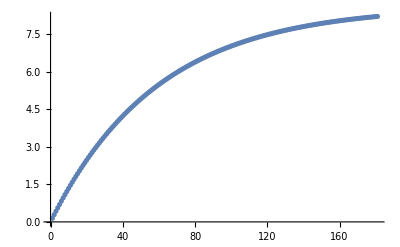

```mathematica
ListPlot[{0.1445143776592257,0.28660701151770057,0.42631848468647193,0.5636887001927146,0.6987568923764438,0.8315616380962447,0.9621408677472182,1.0905318760942895,1.2167713329239758,1.340895293517652,1.4629392089493083,1.5829379362107405,1.7009257481670628,1.8169363433453896,1.93100285555948,2.0431578633730942,2.153433399404764,2.2618609594766377,2.3684715116100086,2.4732955048700997,2.576362878062628,2.6777030682846337,2.777345019332017,2.8753171899661822,2.9716475620421527,3.066363648500473,3.159492501225187,3.251060718770134,3.341094453955767,3.4296194213386673,3.5166609045558825,3.6022437635461957,3.6863924416503755,3.769130972592446,3.8504829873439634,3.930471720873265,4.009120018781612,4.086450343828128,4.162484782345395,4.237245050547533,4.310752500732574,4.383028127380899,4.454092573151473,4.523966134777602,4.592668768863888,4.660220097586039,4.726639414295162,4.791945689028146,4.856157573925693,4.9192934085595645,4.981371225170548,5.042408753818654,5.102423427446996,5.161432386860824,5.21945248562311,5.276500294868102,5.332592108034203,5.387743945517551,5.4419715592476035,5.4952904371860525,5.547715807750343,5.599262644163067,5.649945668728466,5.699779357037274,5.748777942101095,5.796955418417498,5.844325545966982,5.890901854142977,5.936697645615969,5.981726000132884,6.025999778252795,6.069531625020032,6.112333973575731,6.154419048708872,6.1957988703478035,6.236485256993252,6.276489829093812,6.315824012364864,6.354499041051872,6.392525961139004,6.429915633503977,6.466678737020032,6.502825771605933,6.538367061224849,6.573312756832987,6.607672839278804,6.641457122153642,6.67467525459459,6.707336724040379,6.739450858941088,6.771026831422444,6.80207365990548,6.8326002116822835,6.862615205448589,6.892127213793924,6.921144665650032,6.9496758486982575,6.977728911736597,7.005311867007077,7.032432592484128,7.059098834124625,7.085318208080202,7.111098202872508,7.136446181532006,7.161369383700925,7.185874927700982,7.2099698125664435,7.233660920043123,7.256955016553877,7.2798587551311655,7.302378677317227,7.3245212150324095,7.34629269241219,7.3676993276134155,7.388747234590272,7.409442424840491,7.429790809122296,7.449798199142575,7.469470309216764,7.488812757900913,7.5078310695964054,7.52653067612778,7.544916918294117,7.562995047394428,7.580770226727477,7.598247533066473,7.615431958109049,7.632328409902939,7.648941714247771,7.66527661607336,7.681337780794912,7.697129795645516,7.712657170986299,7.727924341594635,7.742935667930764,7.757695437383181,7.77220786549316,7.786477097158754,7.800507207818622,7.814302204616018,7.827866027543266,7.8412025505670675,7.8543155827349445,7.867208869263141,7.8798860926062995,7.892350873509202,7.9046067720408955,7.916657288611481,7.928505864971872,7.9401558851967895,7.951610676651287,7.962873510941084,7.97394760484697,7.984836121243545,7.995542170002574,8.006068808881198,8.016419044395258,8.026595832677987,8.036602080324315,8.046440645221017,8.05611433736296,8.065625919655666,8.07497810870442,8.084173575590166,8.093214946632397,8.102104804139254,8.110845687145057,8.119440092135486,8.127890473760601,8.136199245535915,8.144368780531714,8.152401412050837,8.160299434295089,8.168065103020487,8.175700636181528,8.18320821456466,8.190589982411135,8.197848048029428,8.204984484397391,8.212001329754317,8.218900588183082}]
```

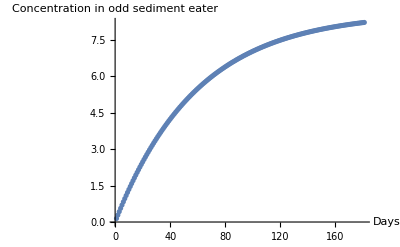

```mathematica
Show[%1,AxesLabel->{HoldForm[Days],HoldForm[Concentration in odd sediment eater]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[{num,ana}]
```

Show::gcomb: Could not combine the graphics objects in Show[{num,ana}].

Show[{num,ana}]

```mathematica
num=ListPlot[{0.23913826245327652,
0.34765071442625767,
0.3968898119775714,
0.4192327660218821,
0.4293712051942479,
0.433971668886198,
0.43605919595236003,
0.43700644160926727}]
```

-Graphics-

```mathematica
c= (Co-q/k) Exp[-k t] +q/k
```

q/k+ⅇ^(-k t) (Co-q/k)

```mathematica
cval = c /. {q->(14716*.000022354),k-> .7515, Co->0}
```

0.43774-0.43774 ⅇ^(-0.7515 t)

```mathematica
ana=Plot[cval,{t,0,8}]
```

-Graphics-

```mathematica
Show[{num,ana}]
```

-Graphics-

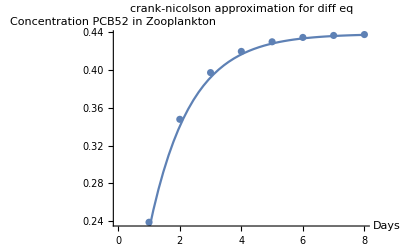

```mathematica
Show[%7,AxesLabel->{HoldForm[Days],HoldForm[Concentration PCB52 in Zooplankton]},PlotLabel->HoldForm[crank-nicolson approximation for diff eq],LabelStyle->{GrayLevel[0]}]
```

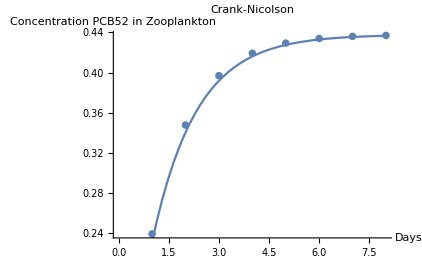

```mathematica
Show[%8,PlotLabel->HoldForm[Crank-Nicolson],LabelStyle->{FontFamily->"Arial",10,RGBColor[0.,0.,0.]}]
```

```mathematica
Export["/Users/toby/Desktop/FishRand/Diff aprox.jpg",%9,"JPEG"]
```

/Users/toby/Desktop/FishRand/Diff aprox.jpg

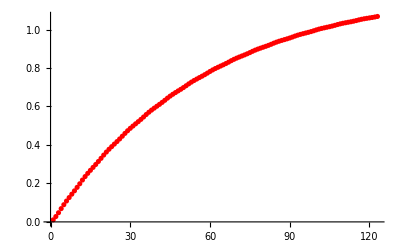

```mathematica
vals = ListPlot[{0.010512524848309711,0.027789322405489623,0.04757701547802561,0.0689696109323856,0.08933314382033526,0.1084897229931632,0.1264362157315654,0.14410391687775334,0.16149286127476803,0.17951296528548152,0.1981990871242244,0.21757417962719772,0.2356135551826903,0.25239077769873214,0.2680058034395293,0.2833476705409306,0.298434482299354,0.31410012322804753,0.3303819876530368,0.34730383503360507,0.3630235340058419,0.37760485252973186,0.39113863430449713,0.40443379308204,0.4175078907395797,0.4311210801300734,0.4453099744754263,0.4600976031076643,0.4737999331461034,0.4864718049485153,0.498195961858404,0.5097115758898153,0.5210357089762508,0.5328643946274947,0.5452335615710135,0.5581656017603456,0.5701139391556932,0.5811256513162532,0.591276438451366,0.6012448358177326,0.6110474706227025,0.6213246280981434,0.6321116418314908,0.6434303496060103,0.6538536865663956,0.6634219809427839,0.6722048093249562,0.6808279866335124,0.6893077621051545,0.6982359509006886,0.7076473691659066,0.7175633728633989,0.7266608055600727,0.7349741273145057,0.7425675905650239,0.7500211727905983,0.7573507946031767,0.76510612909435,0.7733215425227726,0.7820179719343747,0.7899626035719672,0.7971847954407036,0.8037441709211383,0.8101808543499749,0.8165104806179552,0.8232460825981022,0.8304216353968702,0.8380577118351232,0.8450000461589573,0.8512735604178145,0.8569338532803245,0.8624863989611036,0.8679465839319707,0.8737955844048563,0.8800670354008238,0.8867811930670115,0.8928520848316512,0.8983007759239141,0.9031793657460824,0.9079632021314546,0.912667455565217,0.9177456046391539,0.9232309886887278,0.9291435885306359,0.934456808770519,0.9391883613437886,0.9433873032325001,0.9475027890332003,0.9515498014425405,0.9559577374902254,0.9607596794292997,0.9659753686917382,0.9706298350833378,0.9747378750344448,0.9783459003095402,0.9818802919219685,0.9853558692965464,0.9891810918651218,0.993388818361673,0.9979985820862837,1.0020802981257202,1.0056462280385294,1.0087404837175469,1.0117696457941785,1.0147483917373328,1.0180669768855126,1.021758065635123,1.0258410103269797,1.029424751338631,1.0325193462965778,1.03516690748136,1.0377568001779272,1.0403035784323085,1.0431816701219583,1.0464235706774168,1.0500484751053387,1.0531992541338824,1.0558840491914758,1.0581432340054042,1.0603512060607758,1.0625224120941938,1.0650175188735373,1.0678688749227916}, PlotStyle->Red]
```

```mathematica
c= (Co-q/k) Exp[-k t] +q/k
```

q/k+ⅇ^(-k t) (Co-q/k)

```mathematica
cval = c /. {q->(.02101),k-> .01738, Co->0}
```

1.20886-1.20886 ⅇ^(-0.01738 t)

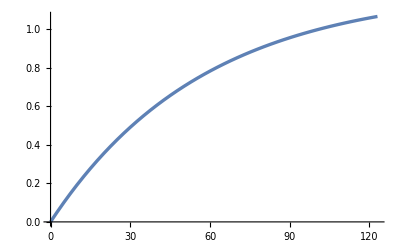

```mathematica
ana=Plot[cval,{t,0,123}, PlotStyle->Thickness[.006]]
```

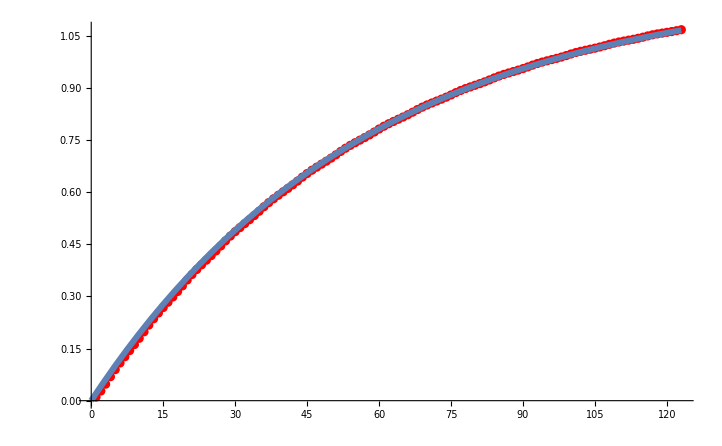

```mathematica
Show[{vals, ana}]
```

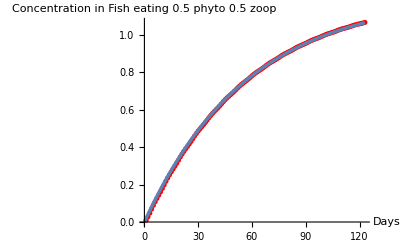

```mathematica
Show[%28,AxesLabel->{HoldForm[Days],HoldForm[Concentration in Fish eating 0.5 phyto 0.5 zoop]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

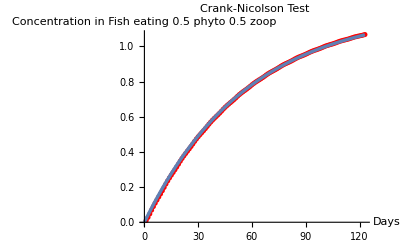

```mathematica
Show[%40,PlotLabel->HoldForm[Crank-Nicolson Test]]
```

```mathematica
Export["/Users/toby/Desktop/FishRand/Crank test day.jpg",%42,"JPEG"]
```

/Users/toby/Desktop/FishRand/Crank test day.jpg

```mathematica
s
```

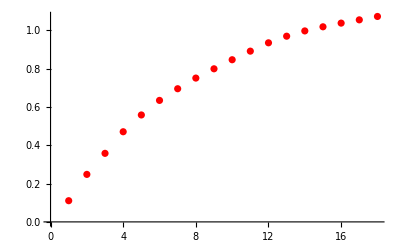

```mathematica
vals2 = ListPlot[{0.11054950879530887,0.24785108943003872,0.35762280509633254,0.4703247257865137,0.5578960627333003,0.6338328536367932,0.6947339258769769,0.7503218690008336,0.7987367484032161,0.8459982183423229,0.8908165887753753,0.9342883341423803,0.9687696848147833,0.996324535707153,1.0178511122247846,1.037072272342535,1.0541031493175772,1.071768455016874} ,PlotStyle-> Red]
```

```mathematica
ana2=Plot[cval,{t,0,123}, PlotStyle->Thickness[.006]]
```

-Graphics-

```mathematica
c2= (Co-q/k) Exp[-k 7t] +q/k
```

q/k+ⅇ^(-7 k t) (Co-q/k)

```mathematica
cval2 = c2 /. {q->(.02101),k-> .01738, Co->0}
```

1.20886-1.20886 ⅇ^(-0.12166 t)

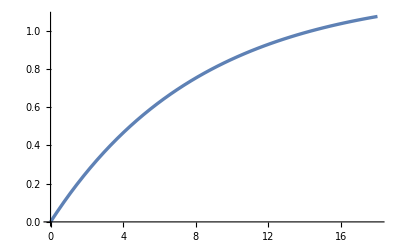

```mathematica
ana2=Plot[cval2,{t,0,18}, PlotStyle->Thickness[.006]]
```

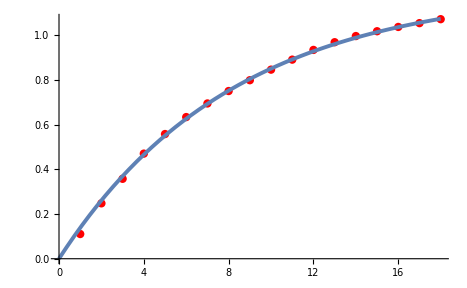

```mathematica
Show[{vals2, ana2}]
```

```mathematica
Show[%39,AxesLabel->{HoldForm[Weeks],HoldForm[Concentration in Fish eating 0.5 phyto 0.5 zoop]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

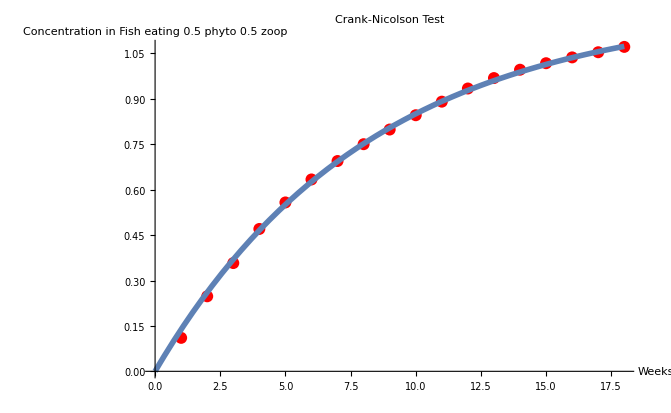

```mathematica
Show[%41,PlotLabel->HoldForm[Crank-Nicolson Test]]
```

```mathematica
Export["/Users/toby/Desktop/FishRand/crank test week.jpg",%43,"JPEG"]
```

/Users/toby/Desktop/FishRand/crank test week.jpg

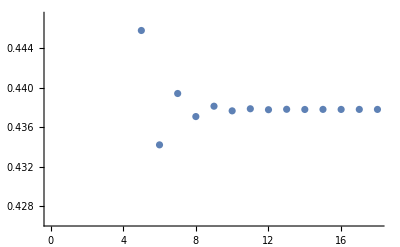

```mathematica
ListPlot[{0.6343895466589572,0.34950949913700147,0.47743821723068236,0.419990329758566,0.4457879756991139,0.4342032409880787,0.4394055016375329,0.4370693656327023,0.43811843483565327,0.4376473380372201,0.4378588895658225,0.43776388987700515,0.4378065505986507,0.4377873933025166,0.43779599611046294,0.43779213291891217,0.4377938677302727,0.43779308869293604}]
```

```mathematica
cval3 = c2 /. {q->(.032899),k-> .7514, Co->0}
```

0.0437836-0.0437836 ⅇ^(-5.2598 t)

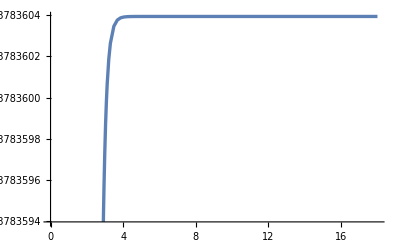

```mathematica
ana3=Plot[cval3,{t,0,18}, PlotStyle->Thickness[.006]]
```

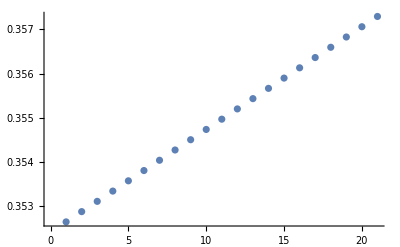

```mathematica
ListPlot[{0.35264087285329604,0.35287342780476627,0.35310598275623645,0.3533385377077067,0.35357109265917686,0.3538036476106471,0.3540362025621173,0.3542687575135875,0.3545013124650577,0.3547338674165279,0.35496642236799814,0.35519897731946837,0.35543153227093854,0.3556640872224088,0.35589664217387895,0.3561291971253492,0.3563617520768194,0.3565943070282896,0.3568268619797598,0.35705941693123,0.35729197188270023}]
```